## Capture Analytics

### Normalize truncated velocity distribution for Evap rate to 1

#### Analytic Expression

When we include this in the Evaporation rate, we will need to factor out the normalization for the MB distribution on the full range and replace it with the below for the restricted / truncated velocity range

```mathematica
fMBnorm = Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),{vχ,0,∞}]]
```

(√(π/2))/(mχ βE)^(3/2)

```mathematica
Assuming[βE mχ/2 vχ^2>0,Integrate[vχ^2 E^(-βE mχ/2 vχ^2),vχ]]
truncedfMBnorm=(%/.vχ->vesc)-(%/.vχ->0)//Simplify
```

-(ⅇ^(-1/2 mχ vχ^2 βE) vχ)/(mχ βE)+(√(π/2) Erf[(√mχ vχ √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

-(ⅇ^(-1/2 mχ vesc^2 βE) vesc)/(mχ βE)+(√(π/2) Erf[(√mχ vesc √βE)/(√2)])/(mχ^(3/2) βE^(3/2))

```mathematica
Clear[x]
EvapRescale =fMBnorm/truncedfMBnorm//FullSimplify//PowerExpand//FullSimplify
("N_(MB, truncated)")/("N_MB")==%/.vesc->x/(√(mχ βE))//FullSimplify//PowerExpand//FullSimplify
x== Subscript[v, esc] √(Subscript[m, χ] Subscript[β, E])
```

1/(-ⅇ^(-1/2 mχ vesc^2 βE) √mχ √(2/π) vesc √βE+Erf[(√mχ vesc √βE)/(√2)])

(N_(MB, truncated))/N_MB==1/(-ⅇ^(-x^2/2) √(2/π) x+Erf[x/(√2)])

x==v_esc √(m_χ β_ⅇ)

1/(-0.0000433788 ⅇ^(-1.4779×10^-9 mχ) √mχ+Erf[0.0000384435 √mχ])

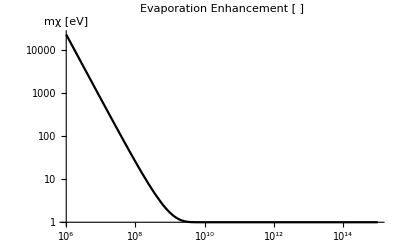

```mathematica
EvapRescale/.vesc->"vesc"/.βE->"βcore"/.EarthRepl/.mχ->mχ("JpereV")/("c")^2/.SIConstRepl//Simplify//PowerExpand
LogLogPlot[%,{mχ,10^6,10^15},PlotLabel->"Evaporation Enhancement [ ]",AxesLabel->"mχ [eV]",PlotStyle->Black]
```

### Analytic Expression for flux / speed dist at Earth

#### Analytic speed dist at Earth - from appendix

Flux density at ∞ is

- n_p_D f_∞(v_∞)  ∫_(toward Earth) dΩ  v.r̂ 

Angular Integral of v . r̂ = v∞ cosθ is

```mathematica
2 π Integrate[Subscript[v, ∞] cosθ^2,{cosθ,0,1}]
```

(2 π v_∞)/3

So just do (2π)/3 times the gravitationally focussed boltzmann distribution, times a factor of number density

ϕ_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 

This is INCOMING flux density, total flux is zero

So the incoming rate is then

ϕ_∞ A_∞ = - n_p_D f_∞(v_∞)  v_∞ (2π)/3 4 π (r_∞)^2

** ** caveat is we need to constrain the integral so that only the particles with impact parameter low enough to reach a given r are included. This expression diverges in the limit r_∞ -> ∞

```mathematica
cosθ = vr/v
```

```mathematica
"The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n."
Integrate[(vr∞)/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->-v∞) - (%/.vr∞->-√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvdistatearth=2 (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand
Print["Factor of 2 from other velocity sign. \n \n Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))"]
```

The f in this expression is normalized to ∫dv f=n. Which is MB times a factor of n.

(√(vesc^2+(vr∞)^2))/(v∞)

((r∞-√(-r^2+(r∞)^2)) √(vesc^2+(v∞)^2))/(r∞ v∞)

(v^2 f[r∞,v∞])/(v∞)^2

Factor of 2 from other velocity sign. 
 
 Note that they normalize as ∫dv f = n but don't inclue the jacobian for velocity volume (v^2) in f. So f is just e^(-β FractionBox[m, 2] SuperscriptBox[v, 2]). This means that this final expression, with the factor of w is simply. f = v^2 e^(-β FractionBox[m, 2] (SuperscriptBox[v, 2] - SubscriptBox[SuperscriptBox[v, 2], esc]))

```mathematica
Integrate[v^2 E^(-β m/2 v^2),{v,0,∞}]//Normal
Normofveldist=A/.Solve[n ==A %,A][[1]]
```

(√(π/2))/(m β)^(3/2)

n √(2/π) (m β)^(3/2)

```mathematica
vdistatearth=Normofveldist unnormedvdistatearth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) v^2 (m β)^(3/2)

```mathematica
natEarth =Integrate[vdistatearth,{v,0,∞}]
```

ConditionalExpression[ⅇ^(1/2 m vesc^2 β) n, Re[m β]>0]

```mathematica
vrintermsofbE=vr/.Solve[bE==rE vperp/vr/.vperp->√(v^2-vr^2),vr][[2]]//Simplify//PowerExpand
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(rE v)/(√(bE^2+rE^2))

#### Flux at Earth - from appendix

```mathematica
ϕE = vdistatearth vrintermsofbE
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n √(2/π) rE v^3 (m β)^(3/2))/(√(bE^2+rE^2))

```mathematica
Integrate[(vr∞)^2/(√((vr∞)^2 + vesc^2)) 1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

(1/2 vr∞ √(vesc^2+(vr∞)^2)+1/2 vesc^2 Log[-vr∞+√(vesc^2+(vr∞)^2)])/(v∞)

1/(2 r∞ v∞)(√(vesc^2+(v∞)^2) (r∞ v∞-√(-r^2+(r∞)^2) √((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2))+r∞ vesc^2 Log[-v∞+√(vesc^2+(v∞)^2)]-r∞ vesc^2 Log[(√(-r^2+(r∞)^2) √(vesc^2+(v∞)^2))/(r∞)-√((v∞)^2-(r^2 (vesc^2+(v∞)^2))/(r∞)^2)])

(v^2 f[r∞,v∞])/(2 v∞)

No factor of 2 here since we only want the incoming flux.

```mathematica
Print["Maybe this is right?"]
Integrate[vr∞  1/(v∞),vr∞]
(%/.vr∞->v∞) - (%/.vr∞->√((v∞)^2 - r^2/(r∞)^2((v∞)^2+vesc^2)))//FullSimplify//PowerExpand//Simplify
unnormedvfluxdistEarth= (r∞)^2/r^2 f[r∞,v∞]D[√(v^2-vesc^2),v]Normal@Series[%,{r∞,∞,2}]/.vesc->√(v^2-(v∞)^2)//PowerExpand//Simplify
Print["No factor of 2 here since we only want the incoming flux."]
```

Maybe this is right?

(vr∞)^2/(2 v∞)

(r^2 (vesc^2+(v∞)^2))/(2 (r∞)^2 v∞)

(v^3 f[r∞,v∞])/(2 (v∞)^2)

No factor of 2 here since we only want the incoming flux.

```mathematica
vfluxdistatearth=Normofveldist unnormedvfluxdistEarth/.f->(#2^2 E^(-β m/2#2^2)&)/.v∞->√(v^2-vesc^2)
```

(ⅇ^(-1/2 m (v^2-vesc^2) β) n v^2 √(v^2-vesc^2) (m β)^(3/2))/(√(2 π))

```mathematica
fluxatEarth=Integrate[vfluxdistatearth,{v,vesc,∞}]//PowerExpand
```

ConditionalExpression[(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π)), Re[vesc]>0&&Im[vesc]==0&&Re[m β]>0]

```mathematica
Normal@fluxatEarth
```

(ⅇ^(1/4 m vesc^2 β) √m n vesc^2 √β BesselK[1,1/4 m vesc^2 β])/(2 √(2 π))

Units here are v n ([mβ] =[1/v^2])

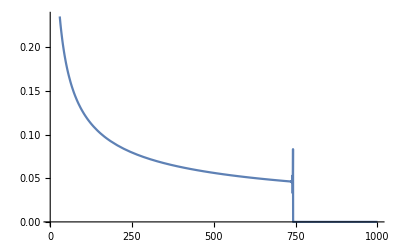

```mathematica
Plot[BesselK[1,x] E^x,{x,1,1000}]
```

(ⅇ^-x √(π/2))/(√x)

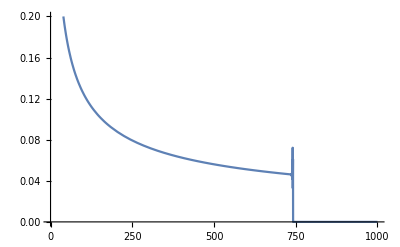

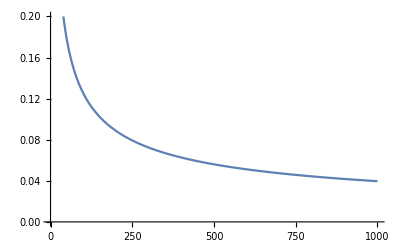

```mathematica
Normal@Series[BesselK[1,x],{x,∞,1}]
Plot[%E^x,{x,1,1000},PlotRange->{0,0.2}]
Plot[√(π/(2 x)),{x,1,1000},PlotRange->{0,0.2}]
```

```mathematica
Series[BesselK[1,x],{x,∞,1}]
```

ⅇ^(-x+O[1/x]^2) (√(π/2) √(1/x)+O[1/x]^(3/2))

So at low temperatures compared to mχ vesc^2 the flux goes as 1/(√ratio)

## Dielectric Analytics

### Electron Contribution to Evaporation Rate

#### Analysis used in notes

Electronic evaporation is suppressed by the degeneracy of the fermi gas. But we want to find an estimate to show that it can be neglected. 

The contribution will only have support near the fermi momentum. We can then expand near the fermi momentum

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

How do we compute energy lost? Intuitively it is from a negative k. But does this make sense? Or is it negative k and negative ω? 

Is it sensible to compute the difference between the pure degenerate and slightly degenerate cases? The dielectric is odd in k and ω. So we should be able to integrate over the forbidden region, then using the fact that ϵ(-k,-ω) = ϵ(k,ω) we can compute as we did before and interpret as the rate for E_(p+k)<E_k (amounts to reinterpretting ω and using evenness in k)

Just use series in small ζ-1, and find the integration region that way.

```mathematica
FOccn = 1/(E^(β(Ek - μ))+1)
Series[FOccn,{Ek,μ,1}]
Assuming[Ek-μ>0,Series[FOccn,{β,∞,1}]]
```

1/(1+ⅇ^(β (Ek-μ)))

1/2-1/4 β (Ek-μ)+O[Ek-μ]^2

1/(1+ⅇ^((Ek-μ) β+O[1/β]^2))

```mathematica
FOccnDζ = 1/(1+ⅇ^(D (-1+ζ^2)))
```

1/(1+ⅇ^(D (-1+ζ^2)))

300

16

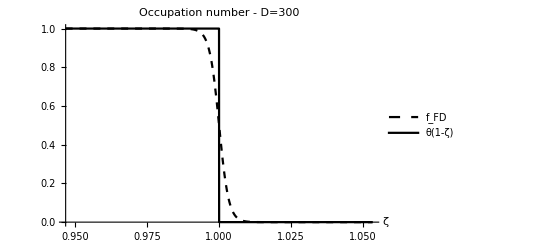

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","θ(1-ζ)"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],
Plot[(HeavisideTheta[1-ζ]),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotStyle->Black,PlotRange->All,AxesLabel->Automatic,Exclusions->None]}]
```

```mathematica
FOccnDζnearkF=Series[FOccnDζ,{ζ,1,1}]//Normal//FullSimplify
```

1/2 (1+D-D ζ)

```mathematica
FOccn /. μ-> EF + π^2/12 1/(D β)
%/.β->D/EF/.Ek->EF ζ^2//Simplify
Series[%,{ζ,1,1}]//Normal//FullSimplify
FOccnDζwμcor=Series[%,{D,∞,1}]//Normal //Simplify
"So we can neglect the change in the chemical potential here. "
```

1/(1+ⅇ^((-EF+Ek-π^2/(12 D β)) β))

1/(1+ⅇ^(-π^2/(12 D)+D (-1+ζ^2)))

(ⅇ^(π^2/(12 D)) (1+ⅇ^(π^2/(12 D))-2 D (-1+ζ)))/((1+ⅇ^(π^2/(12 D)))^2)

1/2+(π^2 (24+π^2 (-1+ζ)))/(1152 D)-1/2 D (-1+ζ)

So we can neglect the change in the chemical potential here.

```mathematica
Solve[FOccnDζnearkF==1,ζ]//Simplify
Solve[FOccnDζnearkF==0,ζ]//Simplify
```

{{ζ→(-1+D)/D}}

{{ζ→1+1/D}}

300

16

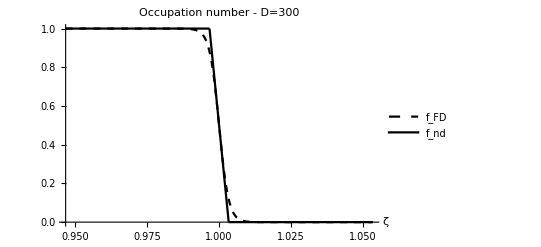

```mathematica
Dtemp = 300
rangerescale=8 * 2
Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-rangerescale/Dtemp,1 + rangerescale/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-rangerescale/Dtemp,1-1/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+1/Dtemp,1+rangerescale/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Compute complex ω RPA dielectric in large D limit

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
"Now compute the dielectric"
δϵRe1 = 1+χ^2/z^2 1/(4 z)(((δχRe1+I δχIm1)/.a->u+z)-((δχRe1+I δχIm1)/.a->u-z))//Simplify
```

Now compute the dielectric

1-1/(4 D z^3)ⅈ χ^2 (ArcTan[(-1+u-z)/uν]-ArcTan[(1+u-z)/uν]-ArcTan[(-1+u+z)/uν]+ArcTan[(1+u+z)/uν]-ⅈ Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+ⅈ Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)])

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D);
#/2 Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal//FullSimplify;
δχRe2=Integrate[%,{ζ,-1,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,2}]//Normal;
δχIm2=Integrate[%,{ζ,-1,1}]
```

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

(-(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)+(-1+3 D) Log[1+(4 a)/((-1+a)^2+uν^2)])/(6 D^2)

1/(6 D^2)((4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)+(-2+6 D) ArcTan[(-1+a)/uν]+(2-6 D) ArcTan[(1+a)/uν])

```mathematica
"Now compute the dielectric"
δϵRe2 = 1+χ^2/z^2 1/(4 z)(((δχRe2+I δχIm2)/.a->u+z)-((δχRe2+I δχIm2)/.a->u-z))//FullSimplify
```

Now compute the dielectric

1+1/(24 D^2 z^3)χ^2 (2 (1/(-1+u+ⅈ uν-z)+1/(1+u+ⅈ uν-z)-1/(-1+u+ⅈ uν+z)-1/(1+u+ⅈ uν+z))+2 ⅈ (-1+3 D) ArcTan[(1+u-z)/uν]+2 ⅈ (-1+3 D) ArcTan[(1-u+z)/uν]+(-1+3 D) (2 ⅈ ArcTan[(-1+u+z)/uν]-2 ⅈ ArcTan[(1+u+z)/uν]-Log[1+(4 (u-z))/(uν^2+(1-u+z)^2)]+Log[1+(4 (u+z))/(uν^2+(-1+u+z)^2)]))

#### Decomposition of 2nd order corrections

```mathematica
(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4)//Apart
2 uν(1/(1+(a-uν)^2)+1/(1+(a+uν)^2))//Apart
 uν(1/(1+I(a-uν))+1/(1-I(a-uν))+1/(1+I(a+uν))+1/(1-I(a+uν)))//Simplify//Apart
```

(2 uν)/(1-2 a+a^2+uν^2)+(2 uν)/(1+2 a+a^2+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

(2 uν)/(1+a^2-2 a uν+uν^2)+(2 uν)/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)//Apart
2((a-1)/(1+(a-uν)^2)+(1+a)/(1+(a+uν)^2))//Apart
```

(2 (-1+a))/(1-2 a+a^2+uν^2)+(2 (1+a))/(1+2 a+a^2+uν^2)

(2 (-1+a))/(1+a^2-2 a uν+uν^2)+(2 (1+a))/(1+a^2+2 a uν+uν^2)

```mathematica
(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2)/.uν->0//Apart
```

2/(-1+a)+2/(1+a)

#### Limits of 2nd order corrections in large and small a

Check that the expansion works for large and small a

```mathematica
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,0,2}]
Series[ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν],{a,∞,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,0,2}]
Series[(4 uν (1+a^2+uν^2))/((-1+a^2)^2+2 (1+a^2) uν^2+uν^4),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

-2 ArcTan[1/uν]+(2 uν a^2)/((1+uν^2)^2)+O[a]^3

-(2 uν)/a^2+O[1/a]^3

(4 uν)/(1+uν^2)-(4 (uν (-3+uν^2)) a^2)/((1+uν^2)^3)+O[a]^3

(4 uν)/a^2+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

```mathematica
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,0,2}]
Series[Log[1+(4 a)/((-1+a)^2+uν^2)],{a,∞,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,0,2}]
Series[(4 a (-1+a^2+uν^2))/(a^4+2 a^2 (-1+uν^2)+(1+uν^2)^2),{a,∞,2}]
"Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant."
```

(4 a)/(1+uν^2)+O[a]^3

4/a+O[1/a]^3

(4 (-1+uν^2) a)/((1+uν^2)^2)+O[a]^3

4/a+O[1/a]^3

Both terms in the expansion scale the same way with large and small a so we don't have to worry about subleading terms becoming dominant.

#### Real RPA limits of above

```mathematica
"The 1st order corrections are straightforward using expressions in the notes."
(Log[(1+a)/(1-a)]/.a->z)-(Log[(1+a)/(1-a)]/.a->-z)
%==2Log[(1+z)/(1-z)]//Simplify//PowerExpand
```

The 1st order corrections are straightforward using expressions in the notes.

-Log[(1-z)/(1+z)]+Log[(1+z)/(1-z)]

True

#### Scattering Phase space

The maximum momentum transfer in ζ we can have in an interaction is

```mathematica
Δζmax = (1+1/D)-(1-1/D)
```

2/D

We have defined fermi function to only have support over this range, since we have defined p = ζ k_F we have that the maximum momentum that can be transfered to the probe from the system for each oscillator is in eV

```mathematica
2/("D")"qF"("ℏ""c")/("JpereV")/.FeTotalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.SiO2Totalparams
2/("D")"qF"("ℏ""c")/("JpereV")/.MgOTotalparams
```

{17.8171,14.5263,11.0565,5.69488,1.12259,0.244832}

{11.2987,6.63264}

{15.7459,11.7913,11.0313,7.13196}

So there is some possibility to evaporate light mass aDM with these kinematics. However, all rates will be suppressed by

```mathematica
"D"/.FeTotalparams
"D"/.SiO2Totalparams
"D"/.MgOTotalparams
```

{322.436,485.073,837.295,3156.08,81222.,1.70758×10^6}

{801.791,2326.72}

{412.839,736.197,841.135,2012.33}

```mathematica
1/("D")/.FeTotalparams
1/("D")/.SiO2Totalparams
1/("D")/.MgOTotalparams
```

{0.00310139,0.00206155,0.00119432,0.000316849,0.0000123119,5.85624×10^-7}

{0.00124721,0.000429789}

{0.00242225,0.00135833,0.00118887,0.000496936}

```mathematica
"Need to recompute the dielectric imposing this kinematic restriction"
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],{D,∞,2}]//Normal
Expandedfndintegrand = ((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D);
# Log[((a+#)^2+uν^2)/((a-#)^2+uν^2)]&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχRe1=Integrate[%,{ζ,0,1}]//FullSimplify

-# (ArcTan[(a+#)/uν]-ArcTan[(a-#)/uν])&;
Series[Expandedfndintegrand/.f->%,{D,∞,1}]//Normal//FullSimplify;
δχIm1=Integrate[%,{ζ,0,1}]//FullSimplify
```

Need to recompute the dielectric imposing this kinematic restriction

∫_0^1 (((1+ζ) f[1-ζ/D])/(2 D)+((1-ζ) f[1+ζ/D])/(2 D))ⅆζ

Log[1+(4 a)/((-1+a)^2+uν^2)]/D

(ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])/D

```mathematica
Series[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D}],{D,∞,2}]//Normal
```

∫_0^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]]
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

0

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D) FOccnDζnearkF f[ζ]ⅆζ)/D

(-f[(-1+D)/D]+D^2 ∫_((-1+D)/D)^(1+1/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

```mathematica
Limit[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D->∞]
"Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand"
f[1]Integrate[D (1-ζ) ,{ζ,1-1/D,1+1/D-2z}]
(*(%/.ζ->1-1/D)//Simplify
(%%/.ζ->1+1/D)//Simplify*)
"Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is"
HoldForm[1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,1-1/D,1+1/D-2z}],D]]
"We can now seperate the integrals"
1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1+1/D-2z}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ],{ζ,0,1-1/D}],D]//Simplify
"Then perform shifts on the variable so that"
1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ-(1/D-2z),{ζ,-1/D+2z,1}],D]//Simplify
-1/D D[Integrate[FOccnDζnearkF f[ζ]/.ζ->ζ+1/D,{ζ,-1/D,1}],D]//Simplify
```

lim_(D→∞) ∫_(1-1/D)^(1+1/D-2 z) 1/2 (1+D-D ζ) f[ζ]ⅆζ

Since f is assumed regular at ζ=1 we have in the limit that D->∞ the integrand

(2 z-2 D z^2) f[1]

Which means that in the expansion of the integral in large D, the 0th order term vanishes. So the next term is

(∂_D ∫_(1-1/D)^(1+1/D-2 z) FOccnDζnearkF f[ζ]ⅆζ)/D

We can now seperate the integrals

(-z f[1+1/D-2 z]+D ∫_0^(1+1/D-2 z) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^2

-(f[(-1+D)/D]+D^2 ∫_0^((-1+D)/D) -1/2 (-1+ζ) f[ζ]ⅆζ)/D^3

Then perform shifts on the variable so that

((-3+D (-1+4 z)) f[-2/D+4 z])/(2 D^3)+1/D(∫_(-1/D+2 z)^1 1/2 (-((-1+2 z+ζ) f[-1/D+2 z+ζ])+((2-D (-1+2 z+ζ)) f'[-1/D+2 z+ζ])/D^2)ⅆζ)

(f[0]+D f[0]-2 D^2 ∫_(-1/D)^1 -((-1+ζ) (D f[1/D+ζ]-f'[1/D+ζ]))/(2 D)ⅆζ)/(2 D^3)

#### Investigate changing slope to conservatively overestimate phase space available

Consider conservatively rescaling the slope of the line to ensure that the phase space that the line doesn’t capture is fermi suppressed.

```mathematica
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1+b/D//Simplify
%/.b->5/.D->10000000//Simplify//N
(*1/(1+E^(2 b))*)E^(-2 b)/.b->5//N
1/(1+ⅇ^(D (-1+ζ^2)))/.ζ->1-b/D//Simplify
1-%/.b->5/.D->10000000//Simplify//N
"So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)"
"So our fermi suppression is about 10^-b"
(Log10@(E^(-2 b)))//Simplify//PowerExpand
N@(Log[10])
```

1/(1+ⅇ^((b (b+2 D))/D))

0.0000453978

0.0000453999

1/(1+ⅇ^((b (b-2 D))/D))

0.000045398

So we see that in the limit of large D a rescaling of D -> D/b gives a fermi suppression at the boundaries of about E^(-2 b)

So our fermi suppression is about 10^-b

-(2 b)/(Log[2]+Log[5])

2.30259

```mathematica
E^-16//N
```

1.12535×10^-7

300

8

2

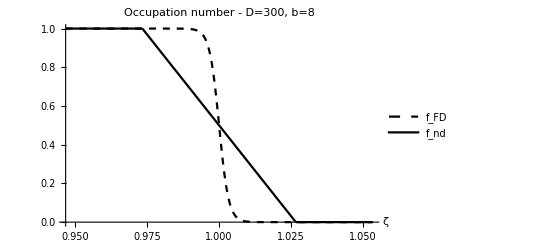

```mathematica
Clear[rangerescale]
Dtemp = 300
sloperescale=8
rangerescale = 2

Show[{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-(rangerescale sloperescale)/Dtemp,1 + (rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Directive[Black,Dashed],PlotLegends->LineLegend[{Directive[Black,Dashed],Black},{"f_FD","f_nd"}],PlotLabel->"Occupation number - D=300, b=8",AxesLabel->Automatic],Plot[(FOccnDζnearkF/.D->D/sloperescale/.D->Dtemp),{ζ,1-sloperescale/Dtemp,1 + sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1-(rangerescale sloperescale)/Dtemp,1-sloperescale/Dtemp},PlotRange->All,PlotStyle->Black],Plot[HeavisideTheta[1-ζ],{ζ,1+sloperescale/Dtemp,1+(rangerescale sloperescale)/Dtemp},PlotRange->All,PlotStyle->Black]}]
```

#### Expand in small and large exponentials

1-x+O[x]^2

1/x+O[1/x]^2

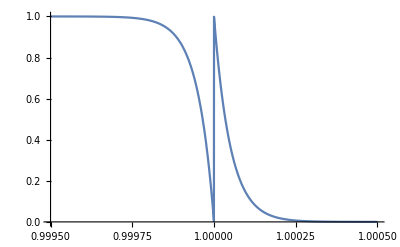

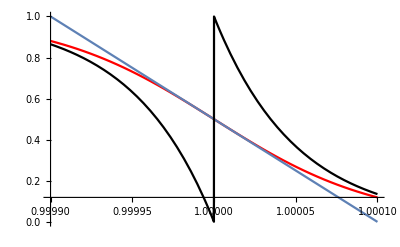

```mathematica
Series[1/(1+x),{x,0,1}]
Series[1/(1+x),{x,∞,1}]
Dtemp = 10000;
Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-5/Dtemp,1 + 5/Dtemp}]
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x)+HeavisideTheta[ζ-1](x^-1)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

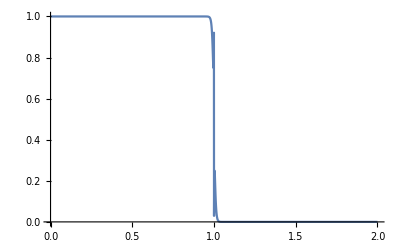

10000

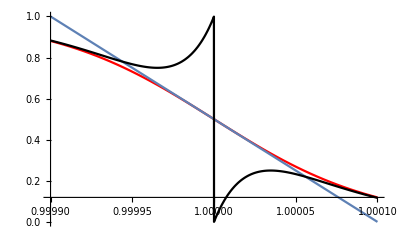

```mathematica
Series[1/(1+x),{x,0,2}]
Series[1/(1+x),{x,∞,2}]
Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->100,{ζ,0,2}]
Dtemp = 10000
Show@{Plot[(1/(1+ⅇ^(D (-1+ζ^2)))/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All,PlotStyle->Red],Plot[(FOccnDζnearkF/.D->Dtemp),{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotRange->All],Plot[HeavisideTheta[1-ζ](1- x+x^2)+HeavisideTheta[ζ-1](x^-1-x^-2)/.x->ⅇ^(D (-1+ζ^2))/.D->Dtemp,{ζ,1-1/Dtemp,1 + 1/Dtemp},PlotStyle->Black]}
```

So our linear approximation is a better fit than expanding in large and small exponentials near the fermi sphere. 

It does givea much better approximation far from the fermi sphere. The question is whether we think the most important contribution to the evaporation rate will be far or close to the fermi sphere. I suppose we can check this by computing the contribution from this expansion. 

The other intriguing part of using this expansion, is that each subsequent term amounts to a change of the value of the degeneracy by an integer, so in principle they could be resummed. So we only need to compute:

```mathematica
Series[1/(1+x),{x,0,2}](*valid between 0 and 1*)
Series[1/(1+x),{x,∞,2}](*valid between 1 and ∞*)
```

1-x+x^2+O[x]^3

1/x-(1/x)^2+O[1/x]^3

```mathematica
Integrate[1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1}]
```

$Aborted

Try integrating by parts for imaginary part

```mathematica
1/2 ζ E^(D(ζ^2-1))Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)](*this is boundary term at 0 and ∞*)
Integrate[1/2 ζ E^(D(ζ^2-1)),ζ]
D[Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],ζ]//FullSimplify(*this is boundary term at 0 and ∞*)
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

1/2 ⅇ^(D (-1+ζ^2)) ζ Log[(uν^2+(a+ζ)^2)/(uν^2+(a-ζ)^2)]

(ⅇ^(-D+D ζ^2))/(4 D)

(4 a (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)

(2 (a-ζ))/(a^2+uν^2-2 a ζ+ζ^2)+(2 (a+ζ))/(a^2+uν^2+2 a ζ+ζ^2)

(a ∫(ⅇ^(-D+D ζ^2) (a^2+uν^2-ζ^2))/(a^4+2 a^2 (uν-ζ) (uν+ζ)+(uν^2+ζ^2)^2)ⅆζ)/D

Try integrating by parts for the real part

```mathematica
- ζ  E^(D(ζ^2-1))(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν])
 Integrate[ζ E^(D(ζ^2-1)),ζ]
D[(ArcTan[(a+ζ)/uν]-ArcTan[(a-ζ)/uν]),ζ]
Apart[%,ζ]
Integrate[%% %%%,ζ]
```

-ⅇ^(D (-1+ζ^2)) ζ (-ArcTan[(a-ζ)/uν]+ArcTan[(a+ζ)/uν])

(ⅇ^(-D+D ζ^2))/(2 D)

1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2))

uν/(a^2+uν^2-2 a ζ+ζ^2)+uν/(a^2+uν^2+2 a ζ+ζ^2)

(∫ⅇ^(-D+D ζ^2) (1/(uν (1+(a-ζ)^2/uν^2))+1/(uν (1+(a+ζ)^2/uν^2)))ⅆζ)/(2 D)

We can differentiate under the integral sign to solve both these integrals.

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,1}]
```

(ⅇ^-D √π Erfi[√D])/(2 √D)

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfi[√D])/(2 √D),f[D],D]//Simplify
```

{{f[D]→-(ⅈ ⅇ^(-a D+ⅈ D uν) π)/(4 √(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π)/(4 √(-1+a+ⅈ uν))+ⅇ^(-D (a+ⅈ uν)) C[1]+ⅇ^(-a D+ⅈ D uν) C[2]-(ⅈ ⅇ^(-a D+ⅈ D uν) π OwenT[ⅈ √2 √D √(-1+a-ⅈ uν),1/(√(-1+a-ⅈ uν))])/(√(-1+a-ⅈ uν))+(ⅈ ⅇ^(-D (a+ⅈ uν)) π OwenT[ⅈ √2 √D √(-1+a+ⅈ uν),1/(√(-1+a+ⅈ uν))])/(√(-1+a+ⅈ uν))}}

```mathematica
Integrate[E^(-D (ζ^2-1)),{ζ,1,∞}]
```

ConditionalExpression[(ⅇ^D √π Erfc[√D])/(2 √D), Re[D]>0]

```mathematica
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν(ⅇ^-D √π Erfc[√D])/(2 √D),f[D],D]//FullSimplify
```

{{f[D]→1/4 ⅇ^(-D (a+ⅈ uν)) (-ⅈ π ((ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν))/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2))/(-1+a+ⅈ uν)^(3/2))+4 (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ π ((ⅇ^(2 ⅈ D uν) √(1-a+ⅈ uν) Erfi[√D √(-1+a-ⅈ uν)])/(√((ⅈ (-1+a)+uν)^2))+(√((ⅈ-ⅈ a+uν)^2) Erfi[√D √(-1+a+ⅈ uν)])/(1-a-ⅈ uν)^(3/2))-4 ⅈ π ((√(-(-1+a+ⅈ uν)^2) OwenT[√2 √D √(1-a-ⅈ uν),1/(√(1-a-ⅈ uν))])/(-1+a+ⅈ uν)^(3/2)+(ⅇ^(2 ⅈ D uν) √(-1+a-ⅈ uν) OwenT[√2 √D √(1-a+ⅈ uν),1/(√(1-a+ⅈ uν))])/(√((ⅈ (-1+a)+uν)^2))))}}

No way that we can sum this over D times an integer. But we can use this to get the non-degenerate limit

```mathematica
Integrate[E^(D (ζ^2-1)),{ζ,0,∞}]//Normal
DSolve[(a^2+uν^2)f[D]+2 a f'[D]+f''[D]==uν%,f[D],D]//FullSimplify
```

(ⅇ^-D √π)/(2 √-D)

{{f[D]→1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))}}

```mathematica
1/(4 √-D)ⅇ^(-D (a+ⅈ uν)) (4 √-D (C[1]+ⅇ^(2 ⅈ D uν) C[2])-ⅈ D √π (ExpIntegralE[1/2,-D (-1+a+ⅈ uν)]-ⅇ^(2 ⅈ D uν) ExpIntegralE[1/2,D-a D+ⅈ D uν]))/.C[1]->0/.C[2]->0/.{a->2,uν->3,D->-100}//N
```

7.13967×10^41+7.25355×10^24 ⅈ

```mathematica
Integrate[E^(D (ζ^2))ζ,{ζ,0,∞}]
```

ConditionalExpression[-1/(2 D), Re[D]<0]

```mathematica
(ζ^2 E^(D (ζ^2-1)))/(u+z+ζ y + I uν)
Integrate[ζ^2 E^(-D (ζ^2-1)),{ζ,0,∞}]
```

(ⅇ^(D (-1+ζ^2)) ζ^2)/(u+ⅈ uν+z+y ζ)

ConditionalExpression[(ⅇ^D √π)/(4 D^(3/2)), Re[D]>0]

```mathematica
DSolve[(u+ⅈ uν+z) f[D]-y  f'[D]==(ⅇ^D √π)/(4 D^(3/2)),f[D],D]//FullSimplify
```

{{f[D]→1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2))}}

```mathematica
Integrate[1/2 ((ⅇ^D √π)/(√D y)+2 ⅇ^((D (u+ⅈ uν+z))/y) C[1]+(ⅇ^((D (u+ⅈ uν+z))/y) π √(u+ⅈ uν-y+z) Erf[(√D √(u+ⅈ uν-y+z))/(√y)])/y^(3/2)),{y,-1,1}]
```

$Aborted

#### Use the form in notes for large and small exponentials

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + i uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+i uν)^2) (CoshIntegral[D (a+i uν)^2]+π Erfi[√D (a+i uν)]+Log[D]-2 Log[-1/(a+i uν)]-Log[D (a+i uν)^2]+SinhIntegral[D (a+i uν)^2]), ]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π Erfi[√D (a+ⅈ uν)]+Log[D]-2 Log[-1/(a+ⅈ uν)]-Log[D (a+ⅈ uν)^2]+SinhIntegral[D (a+ⅈ uν)^2]), (Im[a]+Re[uν]≠0||Im[uν]>Re[a])&&Re[D]>0]

```mathematica
Integrate[(E^(- D ζ^2))/(a - ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2])

1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]+π (-2 ⅈ+Erfi[a √D])+SinhIntegral[a^2 D])

```mathematica
Integrate[(E^(- D ζ^2))/(a + ζ + I uν),{ζ,0,∞}];
%//FullSimplify//PowerExpand//Simplify//Normal
%/.uν->0//FullSimplify
```

-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])

-1/2 ⅇ^(-a^2 D) (CoshIntegral[a^2 D]-π Erfi[a √D]+SinhIntegral[a^2 D])

```mathematica
-1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]-π Erfi[√D (a+ⅈ uν)]+SinhIntegral[D (a+ⅈ uν)^2])-(1/2 ⅇ^(-D (a+ⅈ uν)^2) (CoshIntegral[D (a+ⅈ uν)^2]+π (-2 ⅈ+Erfi[√D (a+ⅈ uν)])+SinhIntegral[D (a+ⅈ uν)^2]))//Simplify
```

ⅇ^(-D (a+ⅈ uν)^2) (ⅈ π-CoshIntegral[D (a+ⅈ uν)^2]-SinhIntegral[D (a+ⅈ uν)^2])

```mathematica
FullSimplify[ExpIntegralEi[z]+1/2(Log[z]+Log[1/z])](*from the ExpIntegralEi properties and relations page on mathematica*)
1/2(Log[z]+Log[1/z])//PowerExpand
```

CoshIntegral[z]+SinhIntegral[z]

0

```mathematica
"So the integral is proportional to"
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]
"The factor of i π is due to the branch cut discontinuity"
```

So the integral is proportional to

ⅇ^(-D (a+ⅈ uν)^2) ExpIntegralEi[D (a+ⅈ uν)^2]

The factor of i π is due to the branch cut discontinuity

2.71828^(-100. ((0.+0.1 ⅈ)+a)^2) ExpIntegralEi[100. ((0.+0.1 ⅈ)+a)^2]

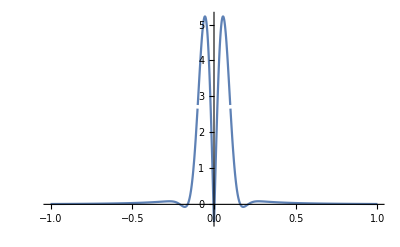

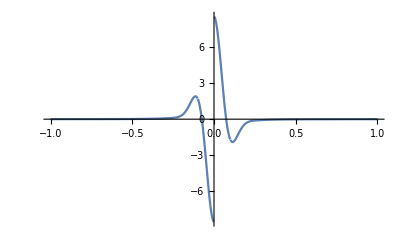

```mathematica
E^(-D(a+I uν)^2)ExpIntegralEi[D(a+I uν)^2]/.D->100/.uν->0.1//N
Plot[Re[%],{a,-1,1},PlotRange->All]
Plot[Im[%%],{a,-1,1},PlotRange->All]
```

```mathematica
"Can we derive this result analytically?"
(E^(- D ζ^2))/(a + uν I + ζ)/.ζ->ζ - (a + uν I )
-(E^(- D ζ^2))/(a + uν I - ζ)/.ζ->ζ + (a + uν I )
HoldForm[Integrate[(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ,{ζ,a + uν I,∞}]]
```

Can we derive this result analytically?

(ⅇ^(-D (-a-ⅈ uν+ζ)^2))/ζ

(ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ

∫_(a+uν ⅈ)^∞ (ⅇ^(-D (a+ⅈ uν+ζ)^2))/ζ ⅆζ

```mathematica
Assuming[z∈Complexes,Integrate[(ⅇ^(-D (ζ)^2))/ζ,{ζ,z,∞}]]
```

ConditionalExpression[1/2 Gamma[0,D z^2], Re[z]>0&&Im[z]==0&&Re[D]>0]

### Mermin Limit to lindhard

#### Limits of Arctan to match onto the Heaviside

```mathematica
Assuming[0<a<1,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[1<a,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
Assuming[a<0,Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Limit[ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ],uτ->∞]
%/.a->1/2
%%/.a->2
%%%/.a->-2
```

(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)

π

0

0

```mathematica
Assuming[0<a<1,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[1<a,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
Assuming[a<0,(√((-1+a)^2) π)/(2-2 a)+(√((1+a)^2) π)/(2+2 a)//Simplify]
```

π

0

Piecewise[{{π, a≥-1}, {0, True}}]

```mathematica
Assuming[0<a<1,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[1<a,π HeavisideTheta[1-Abs[a]]//Simplify]
Assuming[a<0,π HeavisideTheta[1-Abs[a]]//Simplify]
```

π

0

π HeavisideTheta[1+a]

This shows how we match the complex part of the Mermin dielectric onto the Lindhard dielectric. We have simply that

```mathematica
HoldForm@(-Limit[(ArcTan[(1+a)uτ]+ArcTan[(1-a)uτ]),uτ->∞] ==-π HeavisideTheta[1-Abs[a]]) (*Subscript[h, 1]*)
```

-lim_(uτ→∞) (ArcTan[(1+a) uτ]+ArcTan[(1-a) uτ])==-π HeavisideTheta[1-Abs[a]]

#### Mermin to Lindhard Z limits

```mathematica
ReZ=a + 1/2(1-a^2)Log[(1+a)/(1-a)] ;(*Re Z*)
ReϵM=1+1/(4z)((ReZ/.a->u+z)-(ReZ/.a->u-z))
```

1+1/(4 z)(2 z-1/2 (1-(u-z)^2) Log[(1+u-z)/(1-u+z)]+1/2 (1-(u+z)^2) Log[(1+u+z)/(1-u-z)])

```mathematica
ImZ=- I 1/2(1-a^2)π HeavisideTheta[1 - a];(*Im Z*)
ImϵM=1/(4z)((ImZ/.a->u+z)-(ImZ/.a->u-z));
Print["If u+z<1: \n",Assuming[u-z<1&&u+z<1,ImϵM//Simplify]]
Print["If u-z<1<u+z: \n",Assuming[u-z<1<u+z,ImϵM//Simplify]]
Print["If 1<u-z: \n",Assuming[1<u-z&&1<u+z,ImϵM//Simplify]]
```

If u+z<1: 
(ⅈ π u)/2

If u-z<1<u+z: 
-(ⅈ π (-1+u^2-2 u z+z^2))/(8 z)

If 1<u-z: 
0

### Mermin Analytics

#### As in the notes

```mathematica
Integrate[ζ Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

2 a (1+uν ArcTan[(-1+a)/uν]-uν ArcTan[(1+a)/uν])+(1-a^2+uν^2) ArcTanh[(2 a)/(1+a^2+uν^2)]

```mathematica
Integrate[ζ ArcTan[(a+ζ)/uν],{ζ,0,1},Assumptions->{{a,uν}∈ Reals}]
```

ConditionalExpression[1/2 (ArcTan[(1+a)/uν]+(-a^2+uν^2) ArcTan[uν/a]+(a-uν) (a+uν) ArcTan[uν/(1+a)]+uν (-1-a Log[a^2+uν^2]+a Log[(1+a)^2+uν^2])), a>0||a<-1]

```mathematica
-Integrate[(ζ-Abs[a]) ArcTan[ζ/uν],{ζ,Abs[a]-1,Abs[a]+1},Assumptions->{{a,uν}∈ Reals}]//Normal//Simplify//TrigToExp//FullSimplify;
Assuming[a∈Reals&&a>0,%//Simplify//PowerExpand//FullSimplify]
```

1/2 (2 uν+a^2 ArcTan[(1-a)/uν]+(1+uν^2) ArcTan[(-1+a)/uν]+(-1+a^2-uν^2) ArcTan[(1+a)/uν]-2 a uν ArcTanh[(2 a)/(1+a^2+uν^2)])

```mathematica
ArcTanh[(2 a)/(1+a^2+uν^2)]//TrigToExp//PowerExpand
```

-1/2 Log[1-(2 a)/(1+a^2+uν^2)]+1/2 Log[1+(2 a)/(1+a^2+uν^2)]

```mathematica
"check a higher moment too"
Integrate[ζ^2 Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)],{ζ,0,1},Assumptions->{{a,uν}∈ Reals,uν!=0}]
```

check a higher moment too

1/3 (2 a+(6 a^2 uν-2 uν^3) ArcTan[(-1+a)/uν]+4 uν (-3 a^2+uν^2) ArcTan[a/uν]+6 a^2 uν ArcTan[(1+a)/uν]-2 uν^3 ArcTan[(1+a)/uν]-Log[(-1+a)^2+uν^2]+a^3 Log[(-1+a)^2+uν^2]-3 a uν^2 Log[(-1+a)^2+uν^2]-2 a^3 Log[a^2+uν^2]+6 a uν^2 Log[a^2+uν^2]+(1+a^3-3 a uν^2) Log[(1+a)^2+uν^2])

#### Use the Integration by parts method - non-Degenerate Case

```mathematica
(*"Non-degenerate case"
Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)-1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify*)
```

Non-degenerate case

ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])

```mathematica
"non-degenerate case"
-Integrate[E^(-D ζ^2)(1/(a + I uν - ζ)+1/(a + I uν + ζ)),{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
"This is a dawson function!"
```

non-degenerate case

-ⅇ^(-D (a+ⅈ uν)^2) (π Erfi[√D (a+ⅈ uν)]+Log[-a-ⅈ uν]-Log[a+ⅈ uν])

This is a dawson function!

```mathematica
+Log[-a-ⅈ uν]-Log[a+ⅈ uν]//ComplexExpand
(*ArcTan[1+a+I uν]//ComplexExpand*)
- I(Log[a^2] + 2 ArcTan[uν/a])//ComplexExpand
```

ⅈ (Arg[-a-ⅈ uν]-Arg[a+ⅈ uν])

ⅈ (Arg[1-(ⅈ uν)/a]-Arg[1+(ⅈ uν)/a]-Log[a^2])

```mathematica
ComplexExpand[ArcTan[x+I]+ArcTan[x+I]]
```

-Arg[2-ⅈ x]+Arg[ⅈ x]+ⅈ (-1/2 Log[x^2]+1/2 Log[4+x^2])

```mathematica
"non-Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=Integrate[Integrate[ζ E^(-D ζ^2),ζ] Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
```

non-Degenerate case integral bulk

Real part

-1/D a Integrate[(ⅇ^(-D ζ^2) (a^2+uν^2-ζ^2))/((a^2+uν^2-2 a ζ+ζ^2) (a^2+uν^2+2 a ζ+ζ^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

Imaginary part

-1/(2 D)uν Integrate[ⅇ^(-D ζ^2) (-1/(uν^2+(a-ζ)^2)-1/(uν^2+(a+ζ)^2)),ζ,Assumptions→(a|uν)∈ℝ&&uν>0]

```mathematica
"non-degenerate case boundary term"
Integrate[ζ E^(-D ζ^2),ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->∞]
"So in the non-degenerate case, there is no boundary term"
```

non-degenerate case boundary term

-(ⅇ^(-D ζ^2) ArcTanh[ζ/(a+ⅈ uν)])/D

0

0

So in the non-degenerate case, there is no boundary term

```mathematica
Integrate[ζ E^(-D ζ^2),ζ]
```

-(ⅇ^(-D ζ^2))/(2 D)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =Integrate[ζ E^(-D ζ^2),ζ] Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

-(ⅇ^(-D ζ^2) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])/(4 D)

Imaginary part

-(ⅇ^(-D ζ^2) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν]))/(2 D)

```mathematica
"Real part"
Limit[ReBound,ζ->∞,Assumptions->{{a,uν}∈Reals,{D,uν}>0}]
ReBound/.ζ->0
"Imaginary part"
Assuming[{a,uν}∈Reals&&D>0,Limit[ImBound,ζ->∞]]
ImBound/.ζ->0
```

Real part

ConditionalExpression[0, D>0]

0

Imaginary part

0

0

#### Integration by parts method - Degenerate case (and it’s moments)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound = ζ^2/2 Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
ImBound =ζ^2/2 Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(%/.ζ->1)-(%/.ζ->0)
```

degenerate case boundary term

Real part

1/4 ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

1/4 Log[1+(4 a)/((-1+a)^2+uν^2)]

Imaginary part

1/2 ζ^2 (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

1/2 (ArcTan[(-1+a)/uν]-ArcTan[(1+a)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=Integrate[Integrate[ζ ,ζ]Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
"Imaginary part"
ImBulk=Integrate[Integrate[ζ ,ζ]Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(%/.ζ->1)-(%/.ζ->0)//FullSimplify
```

Degenerate case integral bulk

Real part

-a ζ+a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 (-a^2+uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+1/4 (a^2-uν^2) Log[a^2+uν^2+2 a ζ+ζ^2]

-a+a uν ArcTan[(1-a)/uν]+a uν ArcTan[(1+a)/uν]-1/4 (a-uν) (a+uν) (Log[(-1+a)^2+uν^2]-Log[(1+a)^2+uν^2])

Imaginary part

1/2 uν (-2 ζ+(-a^2/uν+uν) ArcTan[(-a+ζ)/uν]+(-a^2/uν+uν) ArcTan[(a+ζ)/uν]-a Log[a^2+uν^2-2 a ζ+ζ^2]+a Log[a^2+uν^2+2 a ζ+ζ^2])

1/2 ((a-uν) (a+uν) ArcTan[(-1+a)/uν]+(-a^2+uν^2) ArcTan[(1+a)/uν]+uν (-2-a Log[(-1+a)^2+uν^2]+a Log[(1+a)^2+uν^2]))

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

a uν ArcTan[(-a+ζ)/uν]+a uν ArcTan[(a+ζ)/uν]+1/4 ζ (-4 a+ζ Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)])-1/4 (a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]-Log[uν^2+(a+ζ)^2])

1/2 ((a^2+ζ^2) ArcTan[(a-ζ)/uν]+uν (-2 ζ+uν ArcTan[(-a+ζ)/uν])-(a^2-uν^2+ζ^2) ArcTan[(a+ζ)/uν]+a uν (-Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

#### Perturbing away from degenerate case

```mathematica
ftilde =Integrate[ζ FOccnDζnearkF,ζ]
```

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3)

```mathematica
"degenerate case boundary term"
"Real part"
ReBound =ftilde Integrate[Re[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
"Imaginary part"
ImBound =ftilde Integrate[Im[1/(a -w + I uν)//ComplexExpand],{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
(*(%/.ζ->1)-(%/.ζ->0)*)
```

degenerate case boundary term

Real part

1/4 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]

Imaginary part

1/2 (ζ^2/2+(D ζ^2)/2-(D ζ^3)/3) (ArcTan[(a-ζ)/uν]-ArcTan[(a+ζ)/uν])

```mathematica
"Degenerate case integral bulk"
"Real part"
ReBulk=-Integrate[ftilde Re[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify,ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
"Imaginary part"
ImBulk=-Integrate[ftilde Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[(1/(a +ζ + I uν)+1/(a -ζ + I uν))]//ComplexExpand//Simplify],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal//Simplify
(*(%/.ζ->1)-(%/.ζ->0)//FullSimplify*)
```

Degenerate case integral bulk

Real part

1/24 (12 a (1+D) ζ-4 a D ζ^2-4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(-a+ζ)/uν]-4 uν (3 a^2 D+3 a (1+D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

Imaginary part

-1/12 uν (-6 (1+D) ζ+2 D ζ^2+((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2) ArcTan[(-a+ζ)/uν])/uν+1/uν(-2 a^3 D-3 a^2 (1+D)+6 a D uν^2+3 (1+D) uν^2) ArcTan[(a+ζ)/uν]+(3 a^2 D-3 a (1+D)-D uν^2) Log[a^2+uν^2-2 a ζ+ζ^2]+(3 a^2 D+3 a (1+D)-D uν^2) Log[a^2+uν^2+2 a ζ+ζ^2])

```mathematica
ReTotal = ReBound+ReBulk//FullSimplify
ImTotal = ImBound+ImBulk//FullSimplify
```

1/24 (12 a (1+D) ζ-4 a D ζ^2+4 uν (-3 a^2 D+3 a (1+D)+D uν^2) ArcTan[(a-ζ)/uν]-4 uν (3 a (1+D+a D)-D uν^2) ArcTan[(a+ζ)/uν]+(-2 a^3 D+3 a^2 (1+D)+6 a D uν^2-3 (1+D) uν^2) Log[uν^2+(a-ζ)^2]+(3+D (3-2 ζ)) ζ^2 Log[1+(4 a ζ)/(uν^2+(a-ζ)^2)]+(-a^2 (3+(3+2 a) D)+3 (1+D+2 a D) uν^2) Log[uν^2+(a+ζ)^2])

1/12 ((2 a^3 D-3 a^2 (1+D)-6 a D uν^2+3 (1+D) uν^2+ζ^2 (3+3 D-2 D ζ)) ArcTan[(a-ζ)/uν]+(2 a^3 D+3 a^2 (1+D)-6 a D uν^2-3 (1+D) uν^2+ζ^2 (-3-3 D+2 D ζ)) ArcTan[(a+ζ)/uν]+uν (2 ζ (3+3 D-D ζ)+(-3 a^2 D+3 a (1+D)+D uν^2) Log[uν^2+(a-ζ)^2]+(-3 a (1+D+a D)+D uν^2) Log[uν^2+(a+ζ)^2]))

```mathematica
ReTotalWbounds=(ReTotal/.ζ->1+1/D- 2 zt/D )-(ReTotal/.ζ->1-1/D )//Simplify;
ImTotalWbounds=(ImTotal/.ζ->1+1/D- 2 zt/D )-(ImTotal/.ζ->1-1/D )//Simplify;
```

```mathematica
Limit[ReTotalWbounds ,D->∞]
Limit[ImTotalWbounds ,D->∞]
```

0

0

```mathematica
Limit[ReTotalWbounds D,D->∞]
Limit[ImTotalWbounds D,D->∞]
```

-1/2 (-1+zt^2) Log[1+(4 a)/((-1+a)^2+uν^2)]

-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&;
Assuming[{zt,z,uν}∈Reals,-1/2 ⅈ (-1+zt^2) (Log[1-(ⅈ (-1+a))/uν]-Log[1+(ⅈ (-1+a))/uν]-Log[1-(ⅈ (1+a))/uν]+Log[1+(ⅈ (1+a))/uν])//ComplexExpand//Simplify]
(-1+zt^2)(-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])
%//ComplexExpand//Simplify
```

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

(-1+zt^2) (-ArcTan[(-1+a)/uν]+ArcTan[(1+a)/uν])

1/2 (-1+zt^2) (Arg[1-(ⅈ (-1+a))/uν]-Arg[1+(ⅈ (-1+a))/uν]-Arg[1-(ⅈ (1+a))/uν]+Arg[1+(ⅈ (1+a))/uν])

```mathematica
ComplexExpand@ArcTan[x]
```

-1/2 Arg[1-ⅈ x]+1/2 Arg[1+ⅈ x]

```mathematica
2 ArcTan[(#-1)/I]+Arg[2-#]&
```

2 ArcTan[(#1-1)/ⅈ]+Arg[2-#1]&

#### ϵnd -> ϵnd_RPA(k,0)

```mathematica
Reh= 1/2 Log[(1+a)/(1-a)] ;(*Re h*)
Reϵnd=1+("χ")^2/(4 z^3)(1/("D")-z)((Reh/.a->u+z)-(Reh/.a->u-z))
%/.u->0//Simplify//PowerExpand
```

1+(χ^2 (1/D-z) (-1/2 Log[(1+u-z)/(1-u+z)]+1/2 Log[(1+u+z)/(1-u-z)]))/(4 z^3)

1+(χ^2 (-1+D z) (2 Log[1-z]-2 Log[1+z]))/(8 D z^3)

```mathematica
Imh=- I π HeavisideTheta[1 - Abs[a]];(*Im h*)
Imϵnd=("χ")^2/(4 z^3)(1/("D")-z)((Imh/.a->u+z)-(Imh/.a->u-z))/.u->0
Print["If z<1: \n",Assuming[-z<1&&z<1,Imϵnd//Simplify]]
Print["If -z<1<+z: \n",Assuming[-z<1<+z,Imϵnd//Simplify]]
(*Print["If 1<-z: \n",Assuming[1<-z&&1<+z,Imϵnd//Simplify]]*)
```

0

If z<1: 
0

If -z<1<+z: 
0

```mathematica
ϵnd0[z]
```

1+(χ^2 (1/D-z) Log[Abs[(1+z)/(1-z)]])/(2 z^3)

```mathematica
ϵRPA0[z]
```

1+(χ^2 (1/2+((1-z^2) Log[(1+z)/Abs[1-z]])/(4 z)))/z^2

#### complex expression for h

```mathematica
Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
```

2 ArcTanh[ζ/(a+ⅈ uν)]

```mathematica
2 ArcTanh[ζ/(a+ⅈ uν)]//ComplexExpand//Simplify
```

1/2 (-2 ⅈ Arg[1-ζ/(a+ⅈ uν)]+2 ⅈ Arg[1+ζ/(a+ⅈ uν)]-Log[(a^2+uν^2-2 a ζ+ζ^2)/(a^2+uν^2)]+Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2)])

#### compare ϵM to ϵMnd

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[-1/ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

0.000214148

```mathematica
ϵM[0.5,0.001,1]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]/.{"χ"->1,"D"->300}
```

106461.+535312. ⅈ

2154.85+1435.9 ⅈ

```mathematica
ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
ϵMnd[0.5,0.001,1]Conjugate[ϵMnd[0.5,0.001,1]]/.{"χ"->1,"D"->300}
```

2.97893×10^11+0. ⅈ

6.70516×10^6+0. ⅈ

```mathematica
Im[-1/ϵM[0.5,0.001,1]]/.{"χ"->1,"D"->300}
Im[ϵMnd[0.5,0.001,1]/(ϵM[0.5,0.001,1]Conjugate[ϵM[0.5,0.001,1]])]/.{"χ"->1,"D"->300}
```

1.79699×10^-6

4.82017×10^-9

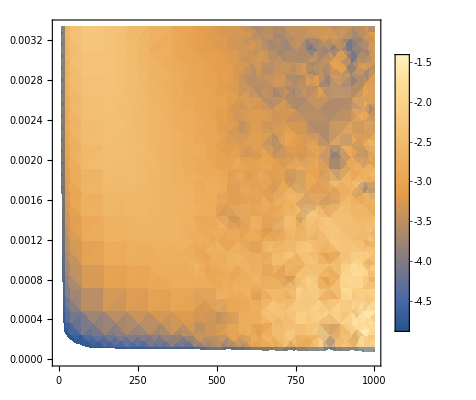

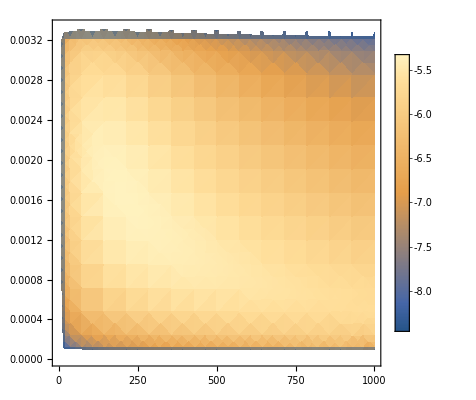

```mathematica
DensityPlot[Log10@Im[-1/ϵM[u,z,1]]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
DensityPlot[Log10@Im[ϵMnd[u,z,1]/(ϵM[u,z,1]Conjugate[ϵM[u,z,1]])]/.{"χ"->1,"D"->300},{u,0,1000},{z,0,1/300},PlotLegends->Automatic]
```

## Scrap

#### more scrap

```mathematica
Integrate
```

Here are some things that would be nice if they work, but currently don’t

```mathematica
"Degenerate case integral proper"
Integrate[Integrate[ζ ,ζ](1/(a -ζ + I uν)1/(a -ζ + I uν)),ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[%]//ComplexExpand//Simplify]
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[%%]//ComplexExpand//Simplify]
```

Degenerate case integral proper

1/2 ((a+ⅈ uν)^2/(a+ⅈ uν-ζ)+ζ+2 (-ⅈ a+uν) ArcTan[uν/(-a+ζ)]+(a+ⅈ uν) Log[a^2+uν^2-2 a ζ+ζ^2])

1/4 (-2 uν Arg[1+(ⅈ uν)/(a-ζ)]+(2 (a^3+a uν^2+2 uν^2 ζ-2 a ζ^2+ζ^3+uν (a^2+uν^2-2 a ζ+ζ^2) Arg[1+(ⅈ uν)/(-a+ζ)]+a (a^2+uν^2-2 a ζ+ζ^2) Log[a^2+uν^2-2 a ζ+ζ^2]))/(a^2+uν^2-2 a ζ+ζ^2))

1/2 (a Arg[1+(ⅈ uν)/(a-ζ)]+(a^2 uν+uν^3-2 a uν ζ-a (uν^2+(a-ζ)^2) Arg[1+(ⅈ uν)/(-a+ζ)]+uν (uν^2+(a-ζ)^2) Log[a^2+uν^2-2 a ζ+ζ^2])/(uν^2+(a-ζ)^2))

```mathematica
"degenerate case boundary term"
Integrate[ζ ,ζ]Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν}∈Reals,uν>0}]//Normal
Limit[%,ζ->0]
Limit[%,ζ->1]
```

degenerate case boundary term

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

0

0

```mathematica
Degenint=ζ^2/2 Integrate[1/(a -w + I uν),{w,-ζ,ζ},Assumptions->{{a,uν,ζ}∈Reals,uν>0}]
"Real part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Re[Degenint]//ComplexExpand//Simplify]
(%/.ζ->1)-(%/.ζ->0)
"Imaginary part"
Assuming[{{a,uν,ζ}∈Reals,uν>0},Im[Degenint]//ComplexExpand]
Assuming[uν>0,(%/.ζ->1)-(%/.ζ->0)//ComplexExpand//FullSimplify]
```

ζ^2 ArcTanh[ζ/(a+ⅈ uν)]

Real part

1/4 ζ^2 Log[(a^2+uν^2+2 a ζ+ζ^2)/(a^2+uν^2-2 a ζ+ζ^2)]

1/4 Log[(1+2 a+a^2+uν^2)/(1-2 a+a^2+uν^2)]

Imaginary part

-1/2 ζ^2 Arg[1-ζ/(a+ⅈ uν)]+1/2 ζ^2 Arg[1+ζ/(a+ⅈ uν)]

1/2 (-Arg[1-1/(a+ⅈ uν)]+Arg[1+1/(a+ⅈ uν)])

Arg is related to Arctan by https://math.stackexchange.com/questions/4293260/argument-of-a-complex-number-as-arctan

#### Scrap

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
Integrate[%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

-1/2 Log[(-1+a)^2+uν^2]+Log[a^2+uν^2]-1/2 Log[(1+a)^2+uν^2]

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand];
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[ζ^2/2%[[1]],ζ,Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify
```

1/4 (-2 ζ^2-4 a uν ArcTan[(a-ζ)/uν]-4 a uν ArcTan[(a+ζ)/uν]-(a-uν) (a+uν) (Log[uν^2+(a-ζ)^2]+Log[uν^2+(a+ζ)^2]))

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[1/(a + I uν - ζ)-1/(a + I uν + ζ)],Im[1/(a + I uν - ζ)-1/(a + I uν + ζ)]}//ComplexExpand]
(*Integrate[ζ^2%[[1]],{ζ,0,1},Assumptions->{{a,uν}∈Reals,uν>0}]//Simplify//PowerExpand//FullSimplify*)
Integrate[E^(-D ζ^2)%[[2]],{ζ,0,∞},Assumptions->{{a,uν,D}∈Reals,{D,uν}>0}]//Simplify//PowerExpand//FullSimplify
```

{a/(uν^2+(a-ζ)^2)-ζ/(uν^2+(a-ζ)^2)-a/(uν^2+(a+ζ)^2)-ζ/(uν^2+(a+ζ)^2),-uν/(uν^2+(a-ζ)^2)+uν/(uν^2+(a+ζ)^2)}

1/2 ⅈ ⅇ^(-D (a+ⅈ uν)^2) (-ExpIntegralEi[D (a+ⅈ uν)^2]-Log[-a-ⅈ uν]+ⅇ^(4 ⅈ a D uν) (ExpIntegralEi[D (a-ⅈ uν)^2]-Log[a-ⅈ uν]+Log[-a+ⅈ uν])+Log[a+ⅈ uν])

```mathematica
Assuming[{a,uν,ζ}∈Reals,{Re[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])],Im[ⅇ^(-D (a+ⅈ uν)^2) (-ⅈ π+ExpIntegralEi[D (a+ⅈ uν)^2])]}//ComplexExpand]//Simplify
```

{ⅇ^(D (-a^2+uν^2)) (Cos[2 a D uν] Re[ExpIntegralEi[D (a+ⅈ uν)^2]]+(-π+Im[ExpIntegralEi[D (a+ⅈ uν)^2]]) Sin[2 a D uν]),-ⅇ^(D (-a^2+uν^2)) (π Cos[2 a D uν]-Cos[2 a D uν] Im[ExpIntegralEi[D (a+ⅈ uν)^2]]+Re[ExpIntegralEi[D (a+ⅈ uν)^2]] Sin[2 a D uν])}

```mathematica
Series[(Log[((a+ζ)^2+uν^2)/((a-ζ)^2+uν^2)]-Log[((ap+ζ)^2+uν^2)/((ap-ζ)^2+uν^2)]),ζ ->∞]
```

(4 a-4 ap)/ζ+O[1/ζ]^3